These data are from:
Basal Metabolic Rate in Carnivores Is Associated with Diet after Controlling for Phylogeny
by Agustí Muñoz-Garcia and Joseph B. Williams
https://www.journals.uchicago.edu/doi/10.1086/432852#_i41

```mathematica
CarnivoreSizeBMR={{10300,2165},{18950,3028},{5444,731},{4100,929},{1215,281},{1819,485},{4725,1195},{1545,385},{1285,304},{624,140},{8854,2997},{29625,9570},{10715,1323},{9000,1301},{13133,2590},{2950,586},{1038,329},{930,362},{834,283},{169,146},{72,87},{5740,421},{3850,486},{3630,573},{860,185},{1287,305},{2688,447},{1160,221},{4847,742},{66957,4049},{136000,8355},{204000,11652},{143000,5559},{540,194},{611,193},{850,148},{14280,541},{2260,435},{1698,358},{1203,286},{4270,414},{3160,365},{2010,265},{137900,11517},{98000,8137},{69000,6160},{37900,4311},{8638,1907},{8350,833},{37175,4246},{2617,472},{1924,431},{10120,1238.69},{10500,1501},{3550,482},{34300,2882},{7710,940}}
```

{{10300,2165},{18950,3028},{5444,731},{4100,929},{1215,281},{1819,485},{4725,1195},{1545,385},{1285,304},{624,140},{8854,2997},{29625,9570},{10715,1323},{9000,1301},{13133,2590},{2950,586},{1038,329},{930,362},{834,283},{169,146},{72,87},{5740,421},{3850,486},{3630,573},{860,185},{1287,305},{2688,447},{1160,221},{4847,742},{66957,4049},{136000,8355},{204000,11652},{143000,5559},{540,194},{611,193},{850,148},{14280,541},{2260,435},{1698,358},{1203,286},{4270,414},{3160,365},{2010,265},{137900,11517},{98000,8137},{69000,6160},{37900,4311},{8638,1907},{8350,833},{37175,4246},{2617,472},{1924,431},{10120,1238.69},{10500,1501},{3550,482},{34300,2882},{7710,940}}

```mathematica
Length[CarnivoreSizeBMR]
```

57

```mathematica
bmrlm =LinearModelFit[Log10@CarnivoreSizeBMR,x,x]
```

FittedModel[0.31655+0.703544 x]

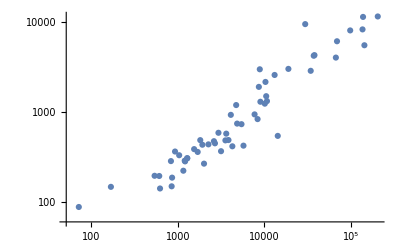

```mathematica
ListLogLogPlot[CarnivoreSizeBMR]
```

The best-fit parameters in Table 4 are clearly log10 transformed, as we confirm above.
So the B0 parameter for carnivore (a = 0.34) is 10^0.34 = 2.07276 kJ/day
1 kJ/day = 0.01157 Watts

```mathematica
10^0.31655003787789404
```

2.07276

```mathematica
Exp[0.7288833984041939]
```

2.07276

```mathematica
2.07*0.01157
```

0.0239499

```mathematica
2.2*10^(-2)
```

0.022

Field metabolic rate for Carnivora from Nagy

```mathematica
FMRB0 = (1.67)*0.01157
```

0.0193219